# Cross Section for QED μ^-e^-→μ^-e^- Process

## Calculating Cross Section

```mathematica
$LoadFeynArts=True;
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

But first, let’s make the font better.

```mathematica
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
```

### Method 1: examples from FeynCalc Website

Take the example on the FeynCalc website.

loading generic model file /Users/isaac/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/isaac/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 1 Classes insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

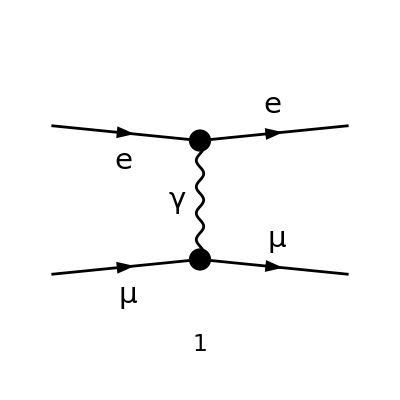

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]},InsertionLevel->{Classes},Restrictions->QEDOnly];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

-(e^2 (φ(OverBar[p3],m_e)).(γ̄)^Lor2.(φ(OverBar[p1],m_e)) (φ(OverBar[p4],m_μ)).(γ̄)^Lor2.(φ(OverBar[p2],m_μ)))/(OverBar[p4]-OverBar[p2])^2

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"],SMP["m_mu"],SMP["m_e"],SMP["m_mu"]];
ampSquared[0]=Simplify[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[FeynAmpDenominatorExplicit[amp[0]*ComplexConjugate[amp[0]]]]]]
```

(2 e^4 (-2 m_e^2 (-2 m_μ^2+s-t+u)+2 m_e^4+2 m_μ^4-2 m_μ^2 (s-t+u)+s^2+u^2))/t^2

### Method 2: Do it directly

Let’s first write down the amplitude.

```mathematica
FCClearScalarProducts[];
SP[p1,p1]=SMP["m_mu"]^2;
SP[p2,p2]=SMP["m_e"]^2;
SP[p3,p3]=SMP["m_mu"]^2;
SP[p4,p4]=SMP["m_e"]^2;
Ma=(-ⅈ e)^2(Spinor[Momentum[p3],SMP["m_mu"]].GA[μ].Spinor[Momentum[p1],SMP["m_mu"]])(-ⅈ MT[μ,ν])/SP[p3-p1,p3-p1](Spinor[Momentum[p4],SMP["m_e"]].GA[ν].Spinor[Momentum[p2],SMP["m_e"]])
MaC=ComplexConjugate[Ma,FCRenameDummyIndices->False]/.{μ->ρ,ν->σ}
```

(ⅈ e^2 (ḡ)^μν (φ(OverBar[p_3],m_μ)).(γ̄)^μ.(φ(OverBar[p_1],m_μ)) (φ(OverBar[p_4],m_e)).(γ̄)^ν.(φ(OverBar[p_2],m_e)))/(OverBar[p_3]-OverBar[p_1])^2

-(ⅈ e^2 (ḡ)^ρσ (φ(OverBar[p_2],m_e)).(γ̄)^σ.(φ(OverBar[p_4],m_e)) (φ(OverBar[p_1],m_μ)).(γ̄)^ρ.(φ(OverBar[p_3],m_μ)))/(OverBar[p_1]-OverBar[p_3])^2

Do the spin sum and average, take the traces, simplify it:

```mathematica
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_mu"],SMP["m_e"],SMP["m_mu"],SMP["m_e"]];
1/4 FermionSpinSum[Ma*MaC]/.DiracTrace->Tr//Contract//Simplify
```

(2 e^4 (-2 m_e^2 (-2 m_μ^2+s-t+u)+2 m_e^4+2 m_μ^4-2 m_μ^2 (s-t+u)+s^2+u^2))/t^2